```mathematica
FileNames["/home/carla/GDC/MUR/*.txt"]
```

{/home/carla/GDC/MUR/MUR_DOJ.txt}

```mathematica
dataDLB=Map[Get[#]&, FileNames["/home/carla/GDC/DLB/*.txt"]][[1]]
dataMUR=Map[Get[#]&, FileNames["/home/carla/GDC/MUR/*.txt"]][[1]];
dataLYE=Map[Get[#]&, FileNames["/home/carla/GDC/LYE/*.txt"]][[1]];
dataPHI=Map[Get[#]&, FileNames["/home/carla/GDC/PHI/*.txt"]][[1]];
dataSED=Map[Get[#]&, FileNames["/home/carla/GDC/SED/*.txt"]][[1]];
dataAUS=Map[Get[#]&, FileNames["/home/carla/GDC/AUS/*.txt"]][[1]];
```

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.000765111},{2.5,0.000765111},{3,0.00609756},{3.5,0.00609756},{4,0.00714286},{4.5,0.00403226},{5,0.00390625},{5.5,0.000821732},{6,0.0223325},{6.5,0.00618132},{7,0.025641},{7.5,0.025641},{8,1.}}

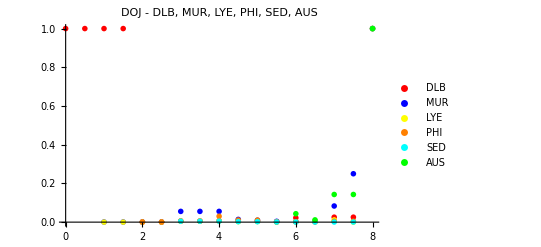

```mathematica
plotDMLPSA=ListPlot[{dataDLB,dataMUR, dataLYE, dataPHI, dataSED, dataAUS},PlotLegends->{"DLB","MUR","LYE", "PHI", "SED", "AUS"},PlotStyle->{Red,Blue,Yellow, Orange, Cyan, Green},PlotRange->All,PlotLabel->"DOJ - DLB, MUR, LYE, PHI, SED, AUS",PlotMarkers->{{"D",12},{"M",12},{"L",12}, {"P",12},{"S",12},{"A",12}}]
```

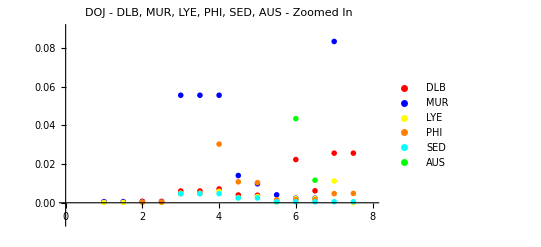

```mathematica
plotDMLPSAZoomedIn=ListPlot[{dataDLB,dataMUR, dataLYE, dataPHI, dataSED, dataAUS},PlotLegends->{"DLB","MUR","LYE", "PHI", "SED", "AUS"},PlotStyle->{Red,Blue,Yellow, Orange, Cyan, Green},PlotRange->{-0.01,0.09},PlotLabel->"DOJ - DLB, MUR, LYE, PHI, SED, AUS - Zoomed In",PlotMarkers->{{"D",12},{"M",12},{"L",12}, {"P",12},{"S",12},{"A",12}}]
```

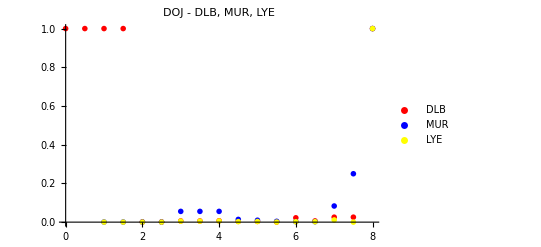

```mathematica
plotDML=ListPlot[{dataDLB,dataMUR, dataLYE},PlotLegends->{"DLB","MUR","LYE"},PlotStyle->{Red,Blue,Yellow},PlotRange->All,PlotLabel->"DOJ - DLB, MUR, LYE",PlotMarkers->{{"D",12},{"M",12},{"L",12}}]
```

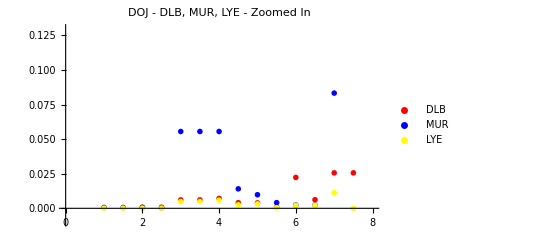

```mathematica
plotDMLZoomedIn=ListPlot[{dataDLB,dataMUR, dataLYE},PlotLegends->{"DLB","MUR","LYE"},PlotStyle->{Red,Blue,Yellow},PlotRange->{-0.01,0.13},PlotLabel->"DOJ - DLB, MUR, LYE - Zoomed In",PlotMarkers->{{"D",12},{"M",12},{"L",12}}]
```

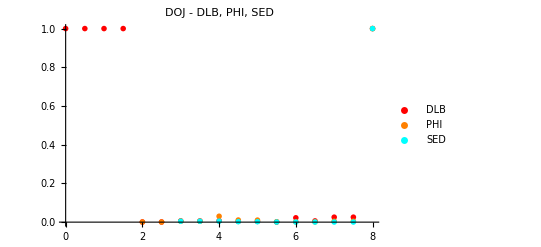

```mathematica
plotDPS=ListPlot[{dataDLB, dataPHI, dataSED},PlotLegends->{"DLB","PHI", "SED"},PlotStyle->{Red,Orange,Cyan},PlotRange->All,PlotLabel->"DOJ - DLB, PHI, SED",PlotMarkers->{{"D",12},{"P",12},{"S",12}}]
```

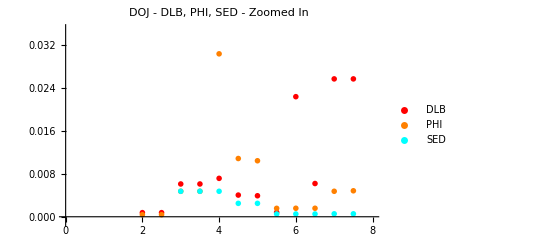

```mathematica
plotDPSZoomedIn=ListPlot[{dataDLB, dataPHI, dataSED},PlotLegends->{"DLB","PHI", "SED"},PlotStyle->{Red,Orange,Cyan},PlotRange->{-0.001,0.035},PlotLabel->"DOJ - DLB, PHI, SED - Zoomed In",PlotMarkers->{{"D",12},{"P",12},{"S",12}}]
```

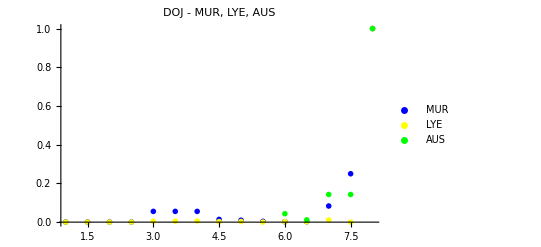

```mathematica
plotMLA=ListPlot[{dataMUR, dataLYE, dataAUS},PlotLegends->{"MUR","LYE", "AUS"},PlotStyle->{Blue,Yellow, Green},PlotRange->All,PlotLabel->"DOJ - MUR, LYE, AUS",PlotMarkers->{{"M",12},{"L",12},{"A",12}}]
```

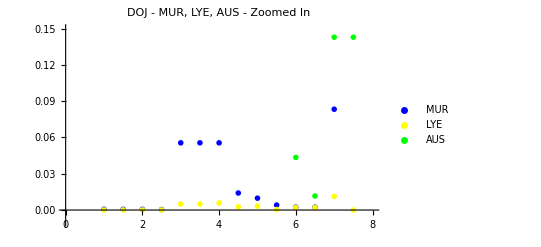

```mathematica
plotMLAZoomedIn=ListPlot[{dataMUR, dataLYE, dataAUS},PlotLegends->{"MUR","LYE", "AUS"},PlotStyle->{Blue,Yellow, Green},PlotRange->{-0.01,0.15},PlotLabel->"DOJ - MUR, LYE, AUS - Zoomed In",PlotMarkers->{{"M",12},{"L",12},{"A",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/ALL_PERS/DOJ"];
Put[<|"DLB"->dataDLB,"MUR"->dataMUR,"LYE"->dataLYE, "PHI"->dataPHI,"SED"->dataSED,"AUS"->dataAUS|>,"DOJ.txt"]
Export["DOJ_DMLPSA.jpeg",plotDMLPSA,ImageSize->850]
Export["DOJ_DMLPSA_ZoomedIn.jpeg",plotDMLPSAZoomedIn,ImageSize->850]
Export["DOJ_DML.jpeg",plotDML,ImageSize->850]
Export["DOJ_DML_ZoomedIn.jpeg",plotDMLZoomedIn,ImageSize->850]
Export["DOJ_DPS.jpeg",plotDPS,ImageSize->850]
Export["DOJ_DPS_ZoomedIn.jpeg",plotDPSZoomedIn,ImageSize->850]
Export["DOJ_MLA.jpeg",plotMLA,ImageSize->850]
Export["DOJ_MLA_ZoomedIn.jpeg",plotMLAZoomedIn,ImageSize->850]
```

DOJ_DMLPSA.jpeg

DOJ_DMLPSA_ZoomedIn.jpeg

DOJ_DML.jpeg

DOJ_DML_ZoomedIn.jpeg

DOJ_DPS.jpeg

DOJ_DPS_ZoomedIn.jpeg

DOJ_MLA.jpeg

DOJ_MLA_ZoomedIn.jpeg